```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=50;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

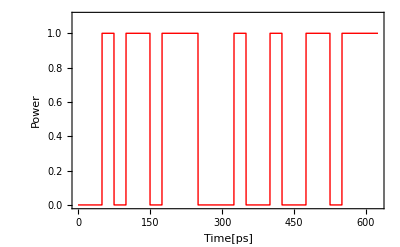

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->20},PlotRange->{0,1.1}]
```

Cos[400000000000000 π t]

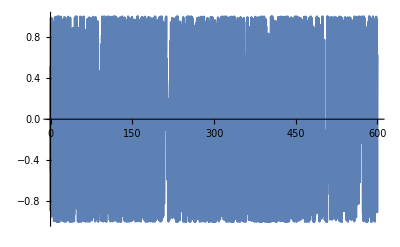

Cos[400000000000000 π t] (If[1/40000000000<t<1/20000000000,0,0]+If[1/20000000000<t<3/40000000000,1,0]+If[3/40000000000<t<1/10000000000,0,0]+If[1/10000000000<t<1/8000000000,1,0]+If[1/8000000000<t<3/20000000000,1,0]+If[3/20000000000<t<7/40000000000,0,0]+If[7/40000000000<t<1/5000000000,1,0]+If[1/5000000000<t<9/40000000000,1,0]+If[9/40000000000<t<1/4000000000,1,0]+If[1/4000000000<t<11/40000000000,0,0]+If[11/40000000000<t<3/10000000000,0,0]+If[3/10000000000<t<13/40000000000,0,0]+If[13/40000000000<t<7/20000000000,1,0]+If[7/20000000000<t<3/8000000000,0,0]+If[3/8000000000<t<1/2500000000,0,0]+If[1/2500000000<t<17/40000000000,1,0]+If[17/40000000000<t<9/20000000000,0,0]+If[9/20000000000<t<19/40000000000,0,0]+If[19/40000000000<t<1/2000000000,1,0]+If[1/2000000000<t<21/40000000000,1,0]+If[21/40000000000<t<11/20000000000,0,0]+If[11/20000000000<t<23/40000000000,1,0]+If[23/40000000000<t<3/5000000000,1,0]+If[3/5000000000<t<1/1600000000,1,0]+If[1/1600000000<t<13/20000000000,1,0])

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t_]= Cos[2*Pi*Fc*t]
Plot[carrier[t], {t,0,600}]
cs[t_]=signal[t]*carrier[t]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) f)/(2 (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) f)/(2 (-40000000000000000000000000000+f^2) π))
```

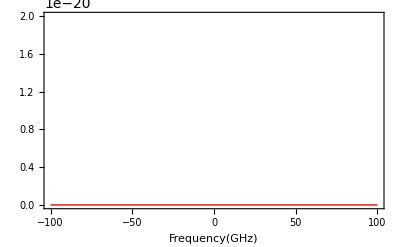

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-1*^2,1*^2},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

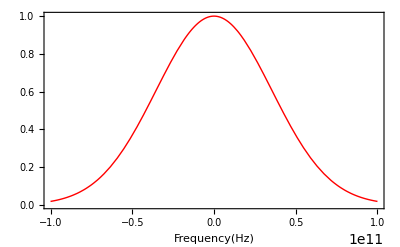

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

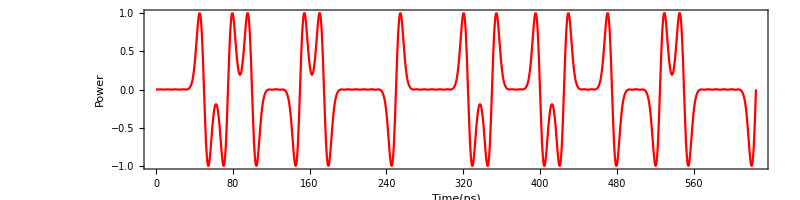

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

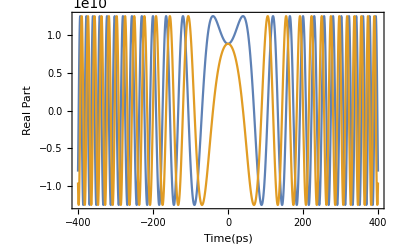

```mathematica
hdis[t_]:=1/(√(2*Pi*β2*L))*Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

-4.96922×10^11+5.77399×10^11 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,7.61788×10^11},{-99.5,7.85126×10^11},{-99.,8.05674×10^11},{-98.5,8.23491×10^11},{-98.,8.38678×10^11},{-97.5,8.51368×10^11},{-97.,8.61726×10^11},{-96.5,8.69941×10^11},{-96.,8.7622×10^11},{-95.5,8.80779×10^11},{-95.,8.83836×10^11},{-94.5,8.856×10^11},{-94.,8.86262×10^11},{-93.5,8.85987×10^11},{-93.,8.84904×10^11},{-92.5,8.83094×10^11},{-92.,8.80593×10^11},{-91.5,8.77376×10^11},{-91.,8.73367×10^11},{-90.5,8.6843×10^11},{-90.,8.62376×10^11},{-89.5,8.5497×10^11},{-89.,8.45937×10^11},{-88.5,8.34971×10^11},{-88.,8.21744×10^11},{-87.5,8.05922×10^11},{-87.,7.87171×10^11},{-86.5,7.65168×10^11},{-86.,7.39616×10^11},{-85.5,7.10249×10^11},{-85.,6.76845×10^11},{-84.5,6.39228×10^11},{-84.,5.97282×10^11},{-83.5,5.50953×10^11},{-83.,5.00256×10^11},{-82.5,4.45281×10^11},{-82.,3.86203×10^11},{-81.5,3.23296×10^11},{-81.,2.56981×10^11},{-80.5,1.87968×10^11},{-80.,1.17954×10^11},{-79.5,5.58437×10^10},{-79.,6.35356×10^10},{-78.5,1.32084×10^11},{-78.,2.09194×10^11},{-77.5,2.88092×10^11},{-77.,3.67063×10^11},{-76.5,4.45114×10^11},{-76.,5.2144×10^11},{-75.5,5.95307×10^11},{-75.,6.6603×10^11},{-74.5,7.32967×10^11},{-74.,7.95523×10^11},{-73.5,8.53157×10^11},{-73.,9.05392×10^11},{-72.5,9.51822×10^11},{-72.,9.92119×10^11},{-71.5,1.02604×10^12},{-71.,1.05344×10^12},{-70.5,1.07426×10^12},{-70.,1.08854×10^12},{-69.5,1.09643×10^12},{-69.,1.09818×10^12},{-68.5,1.09414×10^12},{-68.,1.08474×10^12},{-67.5,1.07053×10^12},{-67.,1.05211×10^12},{-66.5,1.03017×10^12},{-66.,1.00546×10^12},{-65.5,9.78767×10^11},{-65.,9.50889×10^11},{-64.5,9.22625×10^11},{-64.,8.9474×10^11},{-63.5,8.67932×10^11},{-63.,8.42801×10^11},{-62.5,8.19823×10^11},{-62.,7.99327×10^11},{-61.5,7.81484×10^11},{-61.,7.66316×10^11},{-60.5,7.53711×10^11},{-60.,7.43466×10^11},{-59.5,7.35324×10^11},{-59.,7.2903×10^11},{-58.5,7.24377×10^11},{-58.,7.21242×10^11},{-57.5,7.19621×10^11},{-57.,7.19638×10^11},{-56.5,7.21542×10^11},{-56.,7.25692×10^11},{-55.5,7.32514×10^11},{-55.,7.42453×10^11},{-54.5,7.55918×10^11},{-54.,7.73215×10^11},{-53.5,7.94504×10^11},{-53.,8.1976×10^11},{-52.5,8.48765×10^11},{-52.,8.81112×10^11},{-51.5,9.16235×10^11},{-51.,9.53438×10^11},{-50.5,9.91941×10^11},{-50.,1.03091×10^12},{-49.5,1.06949×10^12},{-49.,1.10685×10^12},{-48.5,1.14218×10^12},{-48.,1.17472×10^12},{-47.5,1.20378×10^12},{-47.,1.22872×10^12},{-46.5,1.24902×10^12},{-46.,1.26421×10^12},{-45.5,1.27392×10^12},{-45.,1.27786×10^12},{-44.5,1.27584×10^12},{-44.,1.26775×10^12},{-43.5,1.25356×10^12},{-43.,1.23331×10^12},{-42.5,1.20715×10^12},{-42.,1.17525×10^12},{-41.5,1.13786×10^12},{-41.,1.09531×10^12},{-40.5,1.04792×10^12},{-40.,9.96101×10^11},{-39.5,9.40267×10^11},{-39.,8.80866×10^11},{-38.5,8.1836×10^11},{-38.,7.5323×10^11},{-37.5,6.85968×10^11},{-37.,6.17081×10^11},{-36.5,5.47104×10^11},{-36.,4.76625×10^11},{-35.5,4.06336×10^11},{-35.,3.37159×10^11},{-34.5,2.70536×10^11},{-34.,2.09183×10^11},{-33.5,1.59051×10^11},{-33.,1.32483×10^11},{-32.5,1.41807×10^11},{-32.,1.80051×10^11},{-31.5,2.31957×10^11},{-31.,2.88932×10^11},{-30.5,3.47232×10^11},{-30.,4.05097×10^11},{-29.5,4.61565×10^11},{-29.,5.16031×10^11},{-28.5,5.68064×10^11},{-28.,6.17328×10^11},{-27.5,6.63543×10^11},{-27.,7.06473×10^11},{-26.5,7.45912×10^11},{-26.,7.81682×10^11},{-25.5,8.13635×10^11},{-25.,8.41653×10^11},{-24.5,8.65648×10^11},{-24.,8.85566×10^11},{-23.5,9.01388×10^11},{-23.,9.1313×10^11},{-22.5,9.20848×10^11},{-22.,9.24636×10^11},{-21.5,9.24625×10^11},{-21.,9.20981×10^11},{-20.5,9.13908×10^11},{-20.,9.03641×10^11},{-19.5,8.90444×10^11},{-19.,8.74607×10^11},{-18.5,8.5644×10^11},{-18.,8.3627×10^11},{-17.5,8.14435×10^11},{-17.,7.91279×10^11},{-16.5,7.67148×10^11},{-16.,7.42382×10^11},{-15.5,7.17314×10^11},{-15.,6.92263×10^11},{-14.5,6.6753×10^11},{-14.,6.43397×10^11},{-13.5,6.20124×10^11},{-13.,5.97944×10^11},{-12.5,5.77068×10^11},{-12.,5.57677×10^11},{-11.5,5.3993×10^11},{-11.,5.23959×10^11},{-10.5,5.09872×10^11},{-10.,4.97757×10^11},{-9.5,4.87681×10^11},{-9.,4.79692×10^11},{-8.5,4.73825×10^11},{-8.,4.701×10^11},{-7.5,4.68529×10^11},{-7.,4.69114×10^11},{-6.5,4.71853×10^11},{-6.,4.76744×10^11},{-5.5,4.83779×10^11},{-5.,4.92953×10^11},{-4.5,5.04256×10^11},{-4.,5.17674×10^11},{-3.5,5.33189×10^11},{-3.,5.50767×10^11},{-2.5,5.70361×10^11},{-2.,5.91899×10^11},{-1.5,6.15285×10^11},{-1.,6.40389×10^11},{-0.5,6.6705×10^11},{0.,6.95066×10^11},{0.5,7.24198×10^11},{1.,7.54172×10^11},{1.5,7.84675×10^11},{2.,8.15362×10^11},{2.5,8.45858×10^11},{3.,8.75765×10^11},{3.5,9.04666×10^11},{4.,9.3213×10^11},{4.5,9.57722×10^11},{5.,9.81003×10^11},{5.5,1.00155×10^12},{6.,1.01894×10^12},{6.5,1.03278×10^12},{7.,1.04271×10^12},{7.5,1.04838×10^12},{8.,1.04951×10^12},{8.5,1.04584×10^12},{9.,1.03716×10^12},{9.5,1.02331×10^12},{10.,1.00419×10^12},{10.5,9.79754×10^11},{11.,9.50011×10^11},{11.5,9.15025×10^11},{12.,8.74918×10^11},{12.5,8.29869×10^11},{13.,7.8011×10^11},{13.5,7.25927×10^11},{14.,6.67656×10^11},{14.5,6.05685×10^11},{15.,5.40455×10^11},{15.5,4.72467×10^11},{16.,4.02303×10^11},{16.5,3.30688×10^11},{17.,2.58647×10^11},{17.5,1.88055×10^11},{18.,1.23893×10^11},{18.5,8.45593×10^10},{19.,1.03766×10^11},{19.5,1.60977×10^11},{20.,2.28111×10^11},{20.5,2.97215×10^11},{21.,3.65814×10^11},{21.5,4.32802×10^11},{22.,4.97533×10^11},{22.5,5.59564×10^11},{23.,6.18566×10^11},{23.5,6.74287×10^11},{24.,7.26537×10^11},{24.5,7.75176×10^11},{25.,8.20109×10^11},{25.5,8.61278×10^11},{26.,8.98662×10^11},{26.5,9.32266×10^11},{27.,9.62122×10^11},{27.5,9.88279×10^11},{28.,1.0108×10^12},{28.5,1.02975×10^12},{29.,1.0452×10^12},{29.5,1.05723×10^12},{30.,1.06589×10^12},{30.5,1.07125×10^12},{31.,1.07334×10^12},{31.5,1.07218×10^12},{32.,1.06781×10^12},{32.5,1.0602×10^12},{33.,1.04937×10^12},{33.5,1.03529×10^12},{34.,1.01794×10^12},{34.5,9.97316×10^11},{35.,9.73405×10^11},{35.5,9.46219×10^11},{36.,9.15791×10^11},{36.5,8.82182×10^11},{37.,8.45494×10^11},{37.5,8.05872×10^11},{38.,7.63518×10^11},{38.5,7.18699×10^11},{39.,6.71761×10^11},{39.5,6.23145×10^11},{40.,5.73415×10^11},{40.5,5.23288×10^11},{41.,4.73689×10^11},{41.5,4.25826×10^11},{42.,3.81286×10^11},{42.5,3.42133×10^11},{43.,3.10904×10^11},{43.5,2.903×10^11},{44.,2.8237×10^11},{44.5,2.87476×10^11},{45.,3.03952×10^11},{45.5,3.28867×10^11},{46.,3.59115×10^11},{46.5,3.92059×10^11},{47.,4.25686×10^11},{47.5,4.58519×10^11},{48.,4.89497×10^11},{48.5,5.17862×10^11},{49.,5.43092×10^11},{49.5,5.64849×10^11},{50.,5.82949×10^11},{50.5,5.97343×10^11},{51.,6.08103×10^11},{51.5,6.15414×10^11},{52.,6.19568×10^11},{52.5,6.2095×10^11},{53.,6.20037×10^11},{53.5,6.17381×10^11},{54.,6.13589×10^11},{54.5,6.09307×10^11},{55.,6.05184×10^11},{55.5,6.01839×10^11},{56.,5.9982×10^11},{56.5,5.99563×10^11},{57.,6.01354×10^11},{57.5,6.05311×10^11},{58.,6.1137×10^11},{58.5,6.19296×10^11},{59.,6.28712×10^11},{59.5,6.39127×10^11},{60.,6.4998×10^11},{60.5,6.60675×10^11},{61.,6.70616×10^11},{61.5,6.79231×10^11},{62.,6.8599×10^11},{62.5,6.90421×10^11},{63.,6.92118×10^11},{63.5,6.90743×10^11},{64.,6.86028×10^11},{64.5,6.77777×10^11},{65.,6.65864×10^11},{65.5,6.50227×10^11},{66.,6.30872×10^11},{66.5,6.07866×10^11},{67.,5.81338×10^11},{67.5,5.51478×10^11},{68.,5.18544×10^11},{68.5,4.82866×10^11},{69.,4.44864×10^11},{69.5,4.05079×10^11},{70.,3.6423×10^11},{70.5,3.23314×10^11},{71.,2.83777×10^11},{71.5,2.47803×10^11},{72.,2.1866×10^11},{72.5,2.00699×10^11},{73.,1.98044×10^11},{73.5,2.11941×10^11},{74.,2.3984×10^11},{74.5,2.77586×10^11},{75.,3.21563×10^11},{75.5,3.6924×10^11},{76.,4.18939×10^11},{76.5,4.69535×10^11},{77.,5.20233×10^11},{77.5,5.70444×10^11},{78.,6.19709×10^11},{78.5,6.67652×10^11},{79.,7.13958×10^11},{79.5,7.58355×10^11},{80.,8.00604×10^11},{80.5,8.40488×10^11},{81.,8.77814×10^11},{81.5,9.12406×10^11},{82.,9.44099×10^11},{82.5,9.72746×10^11},{83.,9.98209×10^11},{83.5,1.02036×10^12},{84.,1.03909×10^12},{84.5,1.05428×10^12},{85.,1.06584×10^12},{85.5,1.07369×10^12},{86.,1.07777×10^12},{86.5,1.07802×10^12},{87.,1.0744×10^12},{87.5,1.0669×10^12},{88.,1.05554×10^12},{88.5,1.04035×10^12},{89.,1.02141×10^12},{89.5,9.98819×10^11},{90.,9.72738×10^11},{90.5,9.43357×10^11},{91.,9.10922×10^11},{91.5,8.75732×10^11},{92.,8.38144×10^11},{92.5,7.98576×10^11},{93.,7.57513×10^11},{93.5,7.15506×10^11},{94.,6.73177×10^11},{94.5,6.31217×10^11},{95.,5.90379×10^11},{95.5,5.51468×10^11},{96.,5.15313×10^11},{96.5,4.82721×10^11},{97.,4.54412×10^11},{97.5,4.30926×10^11},{98.,4.12525×10^11},{98.5,3.99112×10^11},{99.,3.9021×10^11},{99.5,3.85004×10^11},{100.,3.82449×10^11},{100.5,3.8141×10^11},{101.,3.80781×10^11},{101.5,3.79575×10^11},{102.,3.76981×10^11},{102.5,3.72382×10^11},{103.,3.65369×10^11},{103.5,3.55735×10^11},{104.,3.43473×10^11},{104.5,3.28776×10^11},{105.,3.12047×10^11},{105.5,2.93904×10^11},{106.,2.75205×10^11},{106.5,2.57059×10^11},{107.,2.40812×10^11},{107.5,2.27959×10^11},{108.,2.19922×10^11},{108.5,2.17691×10^11},{109.,2.21476×10^11},{109.5,2.30607×10^11},{110.,2.43764×10^11},{110.5,2.59358×10^11},{111.,2.75835×10^11},{111.5,2.91831×10^11},{112.,3.06216×10^11},{112.5,3.18086×10^11},{113.,3.26739×10^11},{113.5,3.3165×10^11},{114.,3.32453×10^11},{114.5,3.28924×10^11},{115.,3.20972×10^11},{115.5,3.08628×10^11},{116.,2.9204×10^11},{116.5,2.71461×10^11},{117.,2.47242×10^11},{117.5,2.19824×10^11},{118.,1.89727×10^11},{118.5,1.57539×10^11},{119.,1.23905×10^11},{119.5,8.95219×10^10},{120.,5.51472×10^10},{120.5,2.18524×10^10},{121.,1.31711×10^10},{121.5,4.24574×10^10},{122.,6.99557×10^10},{122.5,9.42128×10^10},{123.,1.14601×10^11},{123.5,1.3063×10^11},{124.,1.41922×10^11},{124.5,1.48223×10^11},{125.,1.49426×10^11},{125.5,1.45616×10^11},{126.,1.37147×10^11},{126.5,1.24796×10^11},{127.,1.10117×10^11},{127.5,9.61508×10^10},{128.,8.83678×10^10},{128.5,9.33845×10^10},{129.,1.13281×10^11},{129.5,1.44457×10^11},{130.,1.82612×10^11},{130.5,2.24781×10^11},{131.,2.68983×10^11},{131.5,3.13742×10^11},{132.,3.5784×10^11},{132.5,4.00205×10^11},{133.,4.39866×10^11},{133.5,4.75945×10^11},{134.,5.07652×10^11},{134.5,5.343×10^11},{135.,5.55313×10^11},{135.5,5.70245×10^11},{136.,5.78801×10^11},{136.5,5.80851×10^11},{137.,5.76465×10^11},{137.5,5.6594×10^11},{138.,5.49844×10^11},{138.5,5.29078×10^11},{139.,5.04948×10^11},{139.5,4.79262×10^11},{140.,4.54424×10^11},{140.5,4.33451×10^11},{141.,4.19795×10^11},{141.5,4.16798×10^11},{142.,4.26809×10^11},{142.5,4.50433×10^11},{143.,4.86452×10^11},{143.5,5.32448×10^11},{144.,5.85583×10^11},{144.5,6.43122×10^11},{145.,7.02652×10^11},{145.5,7.6212×10^11},{146.,8.19797×10^11},{146.5,8.74227×10^11},{147.,9.24187×10^11},{147.5,9.68656×10^11},{148.,1.00679×10^12},{148.5,1.03792×10^12},{149.,1.06151×10^12},{149.5,1.07719×10^12},{150.,1.08472×10^12},{150.5,1.08401×10^12},{151.,1.07507×10^12},{151.5,1.05806×10^12},{152.,1.03322×10^12},{152.5,1.00092×10^12},{153.,9.61617×10^11},{153.5,9.15839×10^11},{154.,8.64201×10^11},{154.5,8.07382×10^11},{155.,7.46112×10^11},{155.5,6.81172×10^11},{156.,6.13385×10^11},{156.5,5.43612×10^11},{157.,4.72759×10^11},{157.5,4.01799×10^11},{158.,3.3181×10^11},{158.5,2.6411×10^11},{159.,2.00576×10^11},{159.5,1.4463×10^11},{160.,1.04018×10^11},{160.5,9.28306×10^10},{161.,1.12867×10^11},{161.5,1.46425×10^11},{162.,1.8137×10^11},{162.5,2.12807×10^11},{163.,2.38547×10^11},{163.5,2.57374×10^11},{164.,2.68489×10^11},{164.5,2.71317×10^11},{165.,2.6543×10^11},{165.5,2.5053×10^11},{166.,2.26432×10^11},{166.5,1.93083×10^11},{167.,1.50607×10^11},{167.5,9.9511×10^10},{168.,4.28495×10^10},{168.5,4.1708×10^10},{169.,1.14419×10^11},{169.5,1.9856×10^11},{170.,2.90066×10^11},{170.5,3.87656×10^11},{171.,4.90237×10^11},{171.5,5.96675×10^11},{172.,7.05762×10^11},{172.5,8.16213×10^11},{173.,9.26675×10^11},{173.5,1.03574×10^12},{174.,1.14197×10^12},{174.5,1.2439×10^12},{175.,1.34009×10^12},{175.5,1.42911×10^12},{176.,1.50959×10^12},{176.5,1.58024×10^12},{177.,1.63986×10^12},{177.5,1.68737×10^12},{178.,1.72184×10^12},{178.5,1.74251×10^12},{179.,1.74881×10^12},{179.5,1.74034×10^12},{180.,1.71694×10^12},{180.5,1.67869×10^12},{181.,1.6259×10^12},{181.5,1.55914×10^12},{182.,1.47923×10^12},{182.5,1.38732×10^12},{183.,1.28484×10^12},{183.5,1.1736×10^12},{184.,1.05586×10^12},{184.5,9.34509×10^11},{185.,8.13342×10^11},{185.5,6.9762×10^11},{186.,5.94939×10^11},{186.5,5.16051×10^11},{187.,4.7362×10^11},{187.5,4.75569×10^11},{188.,5.17499×10^11},{188.5,5.85835×10^11},{189.,6.66884×10^11},{189.5,7.50766×10^11},{190.,8.31035×10^11},{190.5,9.03495×10^11},{191.,9.65358×10^11},{191.5,1.01477×10^12},{192.,1.05057×10^12},{192.5,1.07213×10^12},{193.,1.07933×10^12},{193.5,1.07253×10^12},{194.,1.05254×10^12},{194.5,1.02073×10^12},{195.,9.78983×10^11},{195.5,9.29879×10^11},{196.,8.76748×10^11},{196.5,8.23789×10^11},{197.,7.76089×10^11},{197.5,7.39348×10^11},{198.,7.19092×10^11},{198.5,7.19304×10^11},{199.,7.41083×10^11},{199.5,7.82294×10^11},{200.,8.38465×10^11},{200.5,9.0421×10^11},{201.,9.74286×10^11},{201.5,1.0441×10^12},{202.,1.10982×10^12},{202.5,1.16831×10^12},{203.,1.21708×10^12},{203.5,1.25415×10^12},{204.,1.278×10^12},{204.5,1.28753×10^12},{205.,1.28202×10^12},{205.5,1.26109×10^12},{206.,1.2247×10^12},{206.5,1.17312×10^12},{207.,1.10689×10^12},{207.5,1.02682×10^12},{208.,9.34×10^11},{208.5,8.29703×10^11},{209.,7.1545×10^11},{209.5,5.92987×10^11},{210.,4.64391×10^11},{210.5,3.32467×10^11},{211.,2.02839×10^11},{211.5,1.02222×10^11},{212.,1.39225×10^11},{212.5,2.58601×10^11},{213.,3.87277×10^11},{213.5,5.13956×10^11},{214.,6.35234×10^11},{214.5,7.49226×10^11},{215.,8.54612×10^11},{215.5,9.50413×10^11},{216.,1.03593×10^12},{216.5,1.11072×10^12},{217.,1.17457×10^12},{217.5,1.22753×10^12},{218.,1.26983×10^12},{218.5,1.30193×10^12},{219.,1.32447×10^12},{219.5,1.33822×10^12},{220.,1.34408×10^12},{220.5,1.34302×10^12},{221.,1.33603×10^12},{221.5,1.32409×10^12},{222.,1.3081×10^12},{222.5,1.28884×10^12},{223.,1.26693×10^12},{223.5,1.24281×10^12},{224.,1.21669×10^12},{224.5,1.18859×10^12},{225.,1.15835×10^12},{225.5,1.12564×10^12},{226.,1.09002×10^12},{226.5,1.05098×10^12},{227.,1.00803×10^12},{227.5,9.60673×10^11},{228.,9.08541×10^11},{228.5,8.51365×10^11},{229.,7.89025×10^11},{229.5,7.21567×10^11},{230.,6.4921×10^11},{230.5,5.72349×10^11},{231.,4.91552×10^11},{231.5,4.07569×10^11},{232.,3.21347×10^11},{232.5,2.34144×10^11},{233.,1.48092×10^11},{233.5,7.08696×10^10},{234.,6.14446×10^10},{234.5,1.3082×10^11},{235.,2.07992×10^11},{235.5,2.82558×10^11},{236.,3.5216×10^11},{236.5,4.15545×10^11},{237.,4.71821×10^11},{237.5,5.20307×10^11},{238.,5.60506×10^11},{238.5,5.92092×10^11},{239.,6.1491×10^11},{239.5,6.28978×10^11},{240.,6.3448×10^11},{240.5,6.31762×10^11},{241.,6.21322×10^11},{241.5,6.03797×10^11},{242.,5.79947×10^11},{242.5,5.50631×10^11},{243.,5.16789×10^11},{243.5,4.79412×10^11},{244.,4.39511×10^11},{244.5,3.98088×10^11},{245.,3.56098×10^11},{245.5,3.1442×10^11},{246.,2.73825×10^11},{246.5,2.34959×10^11},{247.,1.98369×10^11},{247.5,1.64592×10^11},{248.,1.34412×10^11},{248.5,1.0945×10^11},{249.,9.31126×10^10},{249.5,9.04339×10^10},{250.,1.03779×10^11},{250.5,1.30115×10^11},{251.,1.65284×10^11},{251.5,2.06642×10^11},{252.,2.52672×10^11},{252.5,3.02324×10^11},{253.,3.54669×10^11},{253.5,4.08758×10^11},{254.,4.63577×10^11},{254.5,5.18037×10^11},{255.,5.70993×10^11},{255.5,6.21263×10^11},{256.,6.67661×10^11},{256.5,7.0902×10^11},{257.,7.44224×10^11},{257.5,7.72238×10^11},{258.,7.92131×10^11},{258.5,8.03114×10^11},{259.,8.04557×10^11},{259.5,7.96027×10^11},{260.,7.77316×10^11},{260.5,7.48487×10^11},{261.,7.09926×10^11},{261.5,6.62438×10^11},{262.,6.07399×10^11},{262.5,5.47035×10^11},{263.,4.84932×10^11},{263.5,4.26898×10^11},{264.,3.82021×10^11},{264.5,3.62274×10^11},{265.,3.77327×10^11},{265.5,4.27226×10^11},{266.,5.0358×10^11},{266.5,5.96709×10^11},{267.,6.992×10^11},{267.5,8.05898×10^11},{268.,9.13132×10^11},{268.5,1.01813×10^12},{269.,1.11868×10^12},{269.5,1.21295×10^12},{270.,1.2994×10^12},{270.5,1.37676×10^12},{271.,1.44394×10^12},{271.5,1.50009×10^12},{272.,1.54455×10^12},{272.5,1.57689×10^12},{273.,1.59686×10^12},{273.5,1.6044×10^12},{274.,1.59965×10^12},{274.5,1.58293×10^12},{275.,1.55473×10^12},{275.5,1.5157×10^12},{276.,1.46664×10^12},{276.5,1.40845×10^12},{277.,1.34216×10^12},{277.5,1.26888×10^12},{278.,1.1898×10^12},{278.5,1.10612×10^12},{279.,1.01911×10^12},{279.5,9.29998×10^11},{280.,8.40025×10^11},{280.5,7.50379×10^11},{281.,6.62196×10^11},{281.5,5.76533×10^11},{282.,4.94356×10^11},{282.5,4.1652×10^11},{283.,3.43755×10^11},{283.5,2.76646×10^11},{284.,2.15617×10^11},{284.5,1.60904×10^11},{285.,1.12528×10^11},{285.5,7.0269×10^10},{286.,3.36835×10^10},{286.5,5.21105×10^9},{287.,2.79788×10^10},{287.5,5.45409×10^10},{288.,8.10583×10^10},{288.5,1.09086×10^11},{289.,1.40015×10^11},{289.5,1.74855×10^11},{290.,2.14181×10^11},{290.5,2.5818×10^11},{291.,3.06736×10^11},{291.5,3.59505×10^11},{292.,4.15984×10^11},{292.5,4.75552×10^11},{293.,5.37503×10^11},{293.5,6.01065×10^11},{294.,6.65415×10^11},{294.5,7.29689×10^11},{295.,7.92991×10^11},{295.5,8.54403×10^11},{296.,9.12991×10^11},{296.5,9.67819×10^11},{297.,1.01795×10^12},{297.5,1.06249×10^12},{298.,1.10053×10^12},{298.5,1.13125×10^12},{299.,1.15388×10^12},{299.5,1.16769×10^12},{300.,1.17208×10^12},{300.5,1.16654×10^12},{301.,1.15066×10^12},{301.5,1.12418×10^12},{302.,1.08696×10^12},{302.5,1.03902×10^12},{303.,9.80542×10^11},{303.5,9.11859×10^11},{304.,8.33474×10^11},{304.5,7.46062×10^11},{305.,6.50472×10^11},{305.5,5.47745×10^11},{306.,4.3916×10^11},{306.5,3.26406×10^11},{307.,2.12346×10^11},{307.5,1.06829×10^11},{308.,8.41566×10^10},{308.5,1.79524×10^11},{309.,2.92372×10^11},{309.5,4.04974×10^11},{310.,5.13431×10^11},{310.5,6.15605×10^11},{311.,7.09832×10^11},{311.5,7.94682×10^11},{312.,8.68903×10^11},{312.5,9.31413×10^11},{313.,9.81309×10^11},{313.5,1.01788×10^12},{314.,1.04064×10^12},{314.5,1.04929×10^12},{315.,1.04379×10^12},{315.5,1.02437×10^12},{316.,9.91494×10^11},{316.5,9.4594×10^11},{317.,8.88819×10^11},{317.5,8.2165×10^11},{318.,7.46482×10^11},{318.5,6.66133×10^11},{319.,5.84624×10^11},{319.5,5.07938×10^11},{320.,4.45011×10^11},{320.5,4.07769×10^11},{321.,4.06943×10^11},{321.5,4.44107×10^11},{322.,5.10549×10^11},{322.5,5.94735×10^11},{323.,6.87501×10^11},{323.5,7.82601×10^11},{324.,8.75817×10^11},{324.5,9.64194×10^11},{325.,1.04557×10^12},{325.5,1.11835×10^12},{326.,1.1813×10^12},{326.5,1.23356×10^12},{327.,1.27453×10^12},{327.5,1.30388×10^12},{328.,1.3215×10^12},{328.5,1.3275×10^12},{329.,1.32219×10^12},{329.5,1.30606×10^12},{330.,1.27976×10^12},{330.5,1.24408×10^12},{331.,1.19993×10^12},{331.5,1.14832×10^12},{332.,1.09032×10^12},{332.5,1.02704×10^12},{333.,9.59616×10^11},{333.5,8.89183×10^11},{334.,8.1683×10^11},{334.5,7.43595×10^11},{335.,6.70436×10^11},{335.5,5.9821×10^11},{336.,5.2766×10^11},{336.5,4.59396×10^11},{337.,3.93892×10^11},{337.5,3.31477×10^11},{338.,2.7234×10^11},{338.5,2.16538×10^11},{339.,1.64009×10^11},{339.5,1.14597×10^11},{340.,6.8081×10^10},{340.5,2.42786×10^10},{341.,1.79172×10^10},{341.5,5.73387×10^10},{342.,9.51915×10^10},{342.5,1.31547×10^11},{343.,1.66577×10^11},{343.5,2.00429×10^11},{344.,2.33229×10^11},{344.5,2.65095×10^11},{345.,2.96158×10^11},{345.5,3.26572×10^11},{346.,3.56531×10^11},{346.5,3.86268×10^11},{347.,4.16058×10^11},{347.5,4.462×10^11},{348.,4.76993×10^11},{348.5,5.08709×10^11},{349.,5.41556×10^11},{349.5,5.75647×10^11},{350.,6.10973×10^11},{350.5,6.47381×10^11},{351.,6.84571×10^11},{351.5,7.22094×10^11},{352.,7.59371×10^11},{352.5,7.9571×10^11},{353.,8.30334×10^11},{353.5,8.62408×10^11},{354.,8.91076×10^11},{354.5,9.15484×10^11},{355.,9.34817×10^11},{355.5,9.48325×10^11},{356.,9.55351×10^11},{356.5,9.55357×10^11},{357.,9.47952×10^11},{357.5,9.32912×10^11},{358.,9.10206×10^11},{358.5,8.80024×10^11},{359.,8.42801×10^11},{359.5,7.99257×10^11},{360.,7.50445×10^11},{360.5,6.97815×10^11},{361.,6.43306×10^11},{361.5,5.89466×10^11},{362.,5.39552×10^11},{362.5,4.97532×10^11},{363.,4.6772×10^11},{363.5,4.53808×10^11},{364.,4.57443×10^11},{364.5,4.77355×10^11},{365.,5.09882×10^11},{365.5,5.50369×10^11},{366.,5.94351×10^11},{366.5,6.38065×10^11},{367.,6.78517×10^11},{367.5,7.13386×10^11},{368.,7.40898×10^11},{368.5,7.59726×10^11},{369.,7.68932×10^11},{369.5,7.67917×10^11},{370.,7.56398×10^11},{370.5,7.344×10^11},{371.,7.0225×10^11},{371.5,6.60593×10^11},{372.,6.10419×10^11},{372.5,5.5314×10^11},{373.,4.90725×10^11},{373.5,4.25999×10^11},{374.,3.63209×10^11},{374.5,3.08996×10^11},{375.,2.73142×10^11},{375.5,2.65922×10^11},{376.,2.8993×10^11},{376.5,3.37229×10^11},{377.,3.97083×10^11},{377.5,4.61416×10^11},{378.,5.25016×10^11},{378.5,5.84474×10^11},{379.,6.37442×10^11},{379.5,6.82233×10^11},{380.,7.1763×10^11},{380.5,7.42784×10^11},{381.,7.57174×10^11},{381.5,7.60586×10^11},{382.,7.53104×10^11},{382.5,7.35124×10^11},{383.,7.0736×10^11},{383.5,6.70883×10^11},{384.,6.27172×10^11},{384.5,5.78209×10^11},{385.,5.2663×10^11},{385.5,4.75937×10^11},{386.,4.30721×10^11},{386.5,3.96606×10^11},{387.,3.79304×10^11},{387.5,3.82397×10^11},{388.,4.05274×10^11},{388.5,4.43555×10^11},{389.,4.91481×10^11},{389.5,5.4381×10^11},{390.,5.96441×10^11},{390.5,6.46337×10^11},{391.,6.91288×10^11},{391.5,7.29717×10^11},{392.,7.60538×10^11},{392.5,7.83076×10^11},{393.,7.97014×10^11},{393.5,8.02361×10^11},{394.,7.99434×10^11},{394.5,7.88842×10^11},{395.,7.71475×10^11},{395.5,7.48491×10^11},{396.,7.213×10^11},{396.5,6.91531×10^11},{397.,6.60986×10^11},{397.5,6.31546×10^11},{398.,6.05041×10^11},{398.5,5.83048×10^11},{399.,5.66668×10^11},{399.5,5.56313×10^11},{400.,5.51605×10^11},{400.5,5.51428×10^11},{401.,5.54128×10^11},{401.5,5.57773×10^11},{402.,5.60403×10^11},{402.5,5.60213×10^11},{403.,5.55656×10^11},{403.5,5.45496×10^11},{404.,5.2882×10^11},{404.5,5.05032×10^11},{405.,4.73838×10^11},{405.5,4.35231×10^11},{406.,3.89489×10^11},{406.5,3.37188×10^11},{407.,2.79289×10^11},{407.5,2.17438×10^11},{408.,1.55114×10^11},{408.5,1.02871×10^11},{409.,9.29299×10^10},{409.5,1.39483×10^11},{410.,2.08933×10^11},{410.5,2.84953×10^11},{411.,3.62562×10^11},{411.5,4.3958×10^11},{412.,5.1471×10^11},{412.5,5.87049×10^11},{413.,6.55948×10^11},{413.5,7.2095×10^11},{414.,7.81771×10^11},{414.5,8.3828×10^11},{415.,8.90479×10^11},{415.5,9.38478×10^11},{416.,9.8247×10^11},{416.5,1.02269×10^12},{417.,1.0594×10^12},{417.5,1.09281×10^12},{418.,1.12308×10^12},{418.5,1.15028×10^12},{419.,1.17436×10^12},{419.5,1.19515×10^12},{420.,1.21233×10^12},{420.5,1.22548×10^12},{421.,1.23407×10^12},{421.5,1.23753×10^12},{422.,1.23522×10^12},{422.5,1.22652×10^12},{423.,1.21086×10^12},{423.5,1.18776×10^12},{424.,1.15683×10^12},{424.5,1.11787×10^12},{425.,1.07082×10^12},{425.5,1.01587×10^12},{426.,9.53411×10^11},{426.5,8.84128×10^11},{427.,8.09×10^11},{427.5,7.29373×10^11},{428.,6.47067×10^11},{428.5,5.64554×10^11},{429.,4.85288×10^11},{429.5,4.14206×10^11},{430.,3.58213×10^11},{430.5,3.25455×10^11},{431.,3.21345×10^11},{431.5,3.43498×10^11},{432.,3.82962×10^11},{432.5,4.3007×10^11},{433.,4.77513×10^11},{433.5,5.20339×10^11},{434.,5.55217×10^11},{434.5,5.79851×10^11},{435.,5.92659×10^11},{435.5,5.92597×10^11},{436.,5.79083×10^11},{436.5,5.51977×10^11},{437.,5.11614×10^11},{437.5,4.58934×10^11},{438.,3.95792×10^11},{438.5,3.25813×10^11},{439.,2.56854×10^11},{439.5,2.07373×10^11},{440.,2.08969×10^11},{440.5,2.70952×10^11},{441.,3.69117×10^11},{441.5,4.84076×10^11},{442.,6.06387×10^11},{442.5,7.30849×10^11},{443.,8.53884×10^11},{443.5,9.72618×10^11},{444.,1.08455×10^12},{444.5,1.18743×10^12},{445.,1.27925×10^12},{445.5,1.35817×10^12},{446.,1.42262×10^12},{446.5,1.47125×10^12},{447.,1.50298×10^12},{447.5,1.517×10^12},{448.,1.51277×10^12},{448.5,1.49008×10^12},{449.,1.44898×10^12},{449.5,1.38985×10^12},{450.,1.31336×10^12},{450.5,1.22043×10^12},{451.,1.1123×10^12},{451.5,9.90404×10^11},{452.,8.56445×10^11},{452.5,7.12311×10^11},{453.,5.60083×10^11},{453.5,4.02051×10^11},{454.,2.40959×10^11},{454.5,8.3527×10^10},{455.,9.72056×10^10},{455.5,2.52072×10^11},{456.,4.05566×10^11},{456.5,5.52286×10^11},{457.,6.89838×10^11},{457.5,8.16312×10^11},{458.,9.30083×10^11},{458.5,1.02979×10^12},{459.,1.11435×10^12},{459.5,1.18299×10^12},{460.,1.23522×10^12},{460.5,1.27092×10^12},{461.,1.29027×10^12},{461.5,1.29385×10^12},{462.,1.28259×10^12},{462.5,1.25781×10^12},{463.,1.22124×10^12},{463.5,1.17503×10^12},{464.,1.12178×10^12},{464.5,1.06454×10^12},{465.,1.00684×10^12},{465.5,9.5256×10^11},{466.,9.0576×10^11},{466.5,8.70238×10^11},{467.,8.48918×10^11},{467.5,8.43177×10^11},{468.,8.5245×10^11},{468.5,8.74361×10^11},{469.,9.05317×10^11},{469.5,9.41249×10^11},{470.,9.78199×10^11},{470.5,1.01266×10^12},{471.,1.04172×10^12},{471.5,1.06306×10^12},{472.,1.07494×10^12},{472.5,1.07611×10^12},{473.,1.0658×10^12},{473.5,1.04364×10^12},{474.,1.00965×10^12},{474.5,9.64168×10^11},{475.,9.07856×10^11},{475.5,8.41667×10^11},{476.,7.66841×10^11},{476.5,6.84923×10^11},{477.,5.97824×10^11},{477.5,5.07992×10^11},{478.,4.18817×10^11},{478.5,3.35608×10^11},{479.,2.67662×10^11},{479.5,2.30275×10^11},{480.,2.36804×10^11},{480.5,2.80906×10^11},{481.,3.44457×10^11},{481.5,4.14351×10^11},{482.,4.83671×10^11},{482.5,5.48773×10^11},{483.,6.0762×10^11},{483.5,6.59042×10^11},{484.,7.02427×10^11},{484.5,7.37574×10^11},{485.,7.64617×10^11},{485.5,7.83986×10^11},{486.,7.96374×10^11},{486.5,8.02709×10^11},{487.,8.04124×10^11},{487.5,8.01908×10^11},{488.,7.97451×10^11},{488.5,7.92167×10^11},{489.,7.87404×10^11},{489.5,7.8433×10^11},{490.,7.83837×10^11},{490.5,7.86455×10^11},{491.,7.92304×10^11},{491.5,8.01103×10^11},{492.,8.12228×10^11},{492.5,8.248×10^11},{493.,8.37794×10^11},{493.5,8.50135×10^11},{494.,8.60789×10^11},{494.5,8.68822×10^11},{495.,8.73442×10^11},{495.5,8.74025×10^11},{496.,8.70121×10^11},{496.5,8.61459×10^11},{497.,8.47936×10^11},{497.5,8.29605×10^11},{498.,8.06658×10^11},{498.5,7.7941×10^11},{499.,7.48275×10^11},{499.5,7.13748×10^11},{500.,6.76383×10^11},{500.5,6.3678×10^11},{501.,5.95568×10^11},{501.5,5.534×10^11},{502.,5.10959×10^11},{502.5,4.68982×10^11},{503.,4.283×10^11},{503.5,3.8991×10^11},{504.,3.55082×10^11},{504.5,3.25456×10^11},{505.,3.03083×10^11},{505.5,2.90234×10^11},{506.,2.88846×10^11},{506.5,2.99792×10^11},{507.,3.22526×10^11},{507.5,3.55433×10^11},{508.,3.96498×10^11},{508.5,4.438×10^11},{509.,4.95685×10^11},{509.5,5.50764×10^11},{510.,6.07843×10^11},{510.5,6.65856×10^11},{511.,7.23821×10^11},{511.5,7.80812×10^11},{512.,8.35944×10^11},{512.5,8.88377×10^11},{513.,9.37315×10^11},{513.5,9.8202×10^11},{514.,1.02182×10^12},{514.5,1.05612×10^12},{515.,1.08442×10^12},{515.5,1.10631×10^12},{516.,1.12152×10^12},{516.5,1.12986×10^12},{517.,1.13129×10^12},{517.5,1.12589×10^12},{518.,1.11387×10^12},{518.5,1.09557×10^12},{519.,1.07144×10^12},{519.5,1.04206×10^12},{520.,1.0081×10^12},{520.5,9.70319×10^11},{521.,9.29563×10^11},{521.5,8.86714×10^11},{522.,8.42679×10^11},{522.5,7.98351×10^11},{523.,7.5457×10^11},{523.5,7.12079×10^11},{524.,6.71469×10^11},{524.5,6.33138×10^11},{525.,5.97248×10^11},{525.5,5.63701×10^11},{526.,5.32144×10^11},{526.5,5.01998×10^11},{527.,4.72517×10^11},{527.5,4.42862×10^11},{528.,4.12187×10^11},{528.5,3.79728×10^11},{529.,3.44886×10^11},{529.5,3.07326×10^11},{530.,2.67132×10^11},{530.5,2.25101×10^11},{531.,1.83485×10^11},{531.5,1.47811×10^11},{532.,1.29778×10^11},{532.5,1.42482×10^11},{533.,1.83827×10^11},{533.5,2.42264×10^11},{534.,3.09975×10^11},{534.5,3.82981×10^11},{535.,4.5904×10^11},{535.5,5.36632×10^11},{536.,6.14561×10^11},{536.5,6.91792×10^11},{537.,7.6739×10^11},{537.5,8.40491×10^11},{538.,9.10294×10^11},{538.5,9.7606×10^11},{539.,1.03712×10^12},{539.5,1.09286×10^12},{540.,1.14277×10^12},{540.5,1.18638×10^12},{541.,1.22333×10^12},{541.5,1.25333×10^12},{542.,1.27618×10^12},{542.5,1.29177×10^12},{543.,1.30007×10^12},{543.5,1.30113×10^12},{544.,1.29507×10^12},{544.5,1.28212×10^12},{545.,1.26256×10^12},{545.5,1.23674×10^12},{546.,1.20507×10^12},{546.5,1.16802×10^12},{547.,1.12612×10^12},{547.5,1.07994×10^12},{548.,1.03007×10^12},{548.5,9.77142×10^11},{549.,9.2181×10^11},{549.5,8.64735×10^11},{550.,8.06585×10^11},{550.5,7.48025×10^11},{551.,6.89707×10^11},{551.5,6.32266×10^11},{552.,5.7631×10^11},{552.5,5.22418×10^11},{553.,4.71135×10^11},{553.5,4.2297×10^11},{554.,3.78408×10^11},{554.5,3.37913×10^11},{555.,3.01952×10^11},{555.5,2.71019×10^11},{556.,2.45648×10^11},{556.5,2.26413×10^11},{557.,2.13853×10^11},{557.5,2.08346×10^11},{558.,2.09954×10^11},{558.5,2.18349×10^11},{559.,2.32895×10^11},{559.5,2.52798×10^11},{560.,2.77258×10^11},{560.5,3.05528×10^11},{561.,3.36931×10^11},{561.5,3.70836×10^11},{562.,4.06638×10^11},{562.5,4.43743×10^11},{563.,4.81555×10^11},{563.5,5.19479×10^11},{564.,5.56922×10^11},{564.5,5.93298×10^11},{565.,6.28041×10^11},{565.5,6.60614×10^11},{566.,6.90515×10^11},{566.5,7.17292×10^11},{567.,7.4055×10^11},{567.5,7.59959×10^11},{568.,7.75264×10^11},{568.5,7.86291×10^11},{569.,7.92951×10^11},{569.5,7.95248×10^11},{570.,7.93277×10^11},{570.5,7.87226×10^11},{571.,7.77378×10^11},{571.5,7.64104×10^11},{572.,7.47859×10^11},{572.5,7.29174×10^11},{573.,7.08638×10^11},{573.5,6.86887×10^11},{574.,6.64573×10^11},{574.5,6.42343×10^11},{575.,6.20792×10^11},{575.5,6.00436×10^11},{576.,5.81657×10^11},{576.5,5.6468×10^11},{577.,5.49538×10^11},{577.5,5.36066×10^11},{578.,5.23919×10^11},{578.5,5.12594×10^11},{579.,5.01486×10^11},{579.5,4.89933×10^11},{580.,4.77275×10^11},{580.5,4.62899×10^11},{581.,4.46281×10^11},{581.5,4.27018×10^11},{582.,4.04862×10^11},{582.5,3.79753×10^11},{583.,3.51863×10^11},{583.5,3.21674×10^11},{584.,2.90109×10^11},{584.5,2.58757×10^11},{585.,2.30228×10^11},{585.5,2.08529×10^11},{586.,1.98796×10^11},{586.5,2.05257×10^11},{587.,2.28414×10^11},{587.5,2.65129×10^11},{588.,3.11269×10^11},{588.5,3.63429×10^11},{589.,4.19171×10^11},{589.5,4.76769×10^11},{590.,5.34949×10^11},{590.5,5.92722×10^11},{591.,6.49289×10^11},{591.5,7.03988×10^11},{592.,7.56259×10^11},{592.5,8.05632×10^11},{593.,8.51714×10^11},{593.5,8.94183×10^11},{594.,9.32782×10^11},{594.5,9.67319×10^11},{595.,9.97659×10^11},{595.5,1.02372×10^12},{596.,1.04548×10^12},{596.5,1.06294×10^12},{597.,1.07618×10^12},{597.5,1.08527×10^12},{598.,1.09034×10^12},{598.5,1.09154×10^12},{599.,1.08904×10^12},{599.5,1.08302×10^12},{600.,1.07366×10^12},{600.5,1.06116×10^12},{601.,1.04573×10^12},{601.5,1.02756×10^12},{602.,1.00684×10^12},{602.5,9.83774×10^11},{603.,9.58543×10^11},{603.5,9.31335×10^11},{604.,9.02332×10^11},{604.5,8.71717×10^11},{605.,8.39673×10^11},{605.5,8.06386×10^11},{606.,7.72052×10^11},{606.5,7.36871×10^11},{607.,7.0106×10^11},{607.5,6.64848×10^11},{608.,6.28483×10^11},{608.5,5.92237×10^11},{609.,5.56402×10^11},{609.5,5.21302×10^11},{610.,4.87286×10^11},{610.5,4.54735×10^11},{611.,4.24055×10^11},{611.5,3.95673×10^11},{612.,3.70018×10^11},{612.5,3.47495×10^11},{613.,3.28449×10^11},{613.5,3.13108×10^11},{614.,3.01539×10^11},{614.5,2.93607×10^11},{615.,2.88971×10^11},{615.5,2.87112×10^11},{616.,2.87394×10^11},{616.5,2.89133×10^11},{617.,2.91655×10^11},{617.5,2.94347×10^11},{618.,2.96676×10^11},{618.5,2.98202×10^11},{619.,2.98579×10^11},{619.5,2.97547×10^11},{620.,2.9493×10^11},{620.5,2.90625×10^11},{621.,2.84598×10^11},{621.5,2.76878×10^11},{622.,2.67554×10^11},{622.5,2.5677×10^11},{623.,2.44726×10^11},{623.5,2.31675×10^11},{624.,2.17921×10^11},{624.5,2.0382×10^11},{625.,1.89779×10^11},{625.5,1.76248×10^11},{626.,1.63704×10^11},{626.5,1.52624×10^11},{627.,1.43435×10^11},{627.5,1.36437×10^11},{628.,1.31728×10^11},{628.5,1.2916×10^11},{629.,1.28346×10^11},{629.5,1.28733×10^11},{630.,1.29704×10^11},{630.5,1.30664×10^11},{631.,1.31099×10^11},{631.5,1.30606×10^11},{632.,1.28907×10^11},{632.5,1.25848×10^11},{633.,1.21415×10^11},{633.5,1.15741×10^11},{634.,1.09142×10^11},{634.5,1.02165×10^11},{635.,9.56407×10^10},{635.5,9.07221×10^10},{636.,8.87664×10^10},{636.5,9.09629×10^10},{637.,9.78277×10^10},{637.5,1.09025×10^11},{638.,1.23679×10^11},{638.5,1.4079×10^11},{639.,1.59468×10^11},{639.5,1.78984×10^11},{640.,1.98759×10^11},{640.5,2.18329×10^11},{641.,2.37328×10^11},{641.5,2.55471×10^11},{642.,2.72546×10^11},{642.5,2.88416×10^11},{643.,3.03012×10^11},{643.5,3.16333×10^11},{644.,3.28451×10^11},{644.5,3.395×10^11},{645.,3.49679×10^11},{645.5,3.59239×10^11},{646.,3.68471×10^11},{646.5,3.77692×10^11},{647.,3.87225×10^11},{647.5,3.97377×10^11},{648.,4.08414×10^11},{648.5,4.20546×10^11},{649.,4.33909×10^11},{649.5,4.48557×10^11},{650.,4.64464×10^11},{650.5,4.81531×10^11},{651.,4.99597×10^11},{651.5,5.18462×10^11},{652.,5.37894×10^11},{652.5,5.57658×10^11},{653.,5.77522×10^11},{653.5,5.97276×10^11},{654.,6.16735×10^11},{654.5,6.35754×10^11},{655.,6.54223×10^11},{655.5,6.72074×10^11},{656.,6.89275×10^11},{656.5,7.05828×10^11},{657.,7.21762×10^11},{657.5,7.37124×10^11},{658.,7.51973×10^11},{658.5,7.66364×10^11},{659.,7.80343×10^11},{659.5,7.93936×10^11},{660.,8.07138×10^11},{660.5,8.19912×10^11},{661.,8.32179×10^11},{661.5,8.43819×10^11},{662.,8.54674×10^11},{662.5,8.64546×10^11},{663.,8.73207×10^11},{663.5,8.80403×10^11},{664.,8.85865×10^11},{664.5,8.89313×10^11},{665.,8.90469×10^11},{665.5,8.89062×10^11},{666.,8.84836×10^11},{666.5,8.77559×10^11},{667.,8.67024×10^11},{667.5,8.53059×10^11},{668.,8.35526×10^11},{668.5,8.14327×10^11},{669.,7.89403×10^11},{669.5,7.60736×10^11},{670.,7.28347×10^11},{670.5,6.92299×10^11},{671.,6.52691×10^11},{671.5,6.09661×10^11},{672.,5.6338×10^11},{672.5,5.14056×10^11},{673.,4.61927×10^11},{673.5,4.07265×10^11},{674.,3.50384×10^11},{674.5,2.91648×10^11},{675.,2.31519×10^11},{675.5,1.70701×10^11},{676.,1.10776×10^11},{676.5,5.86409×10^10},{677.,5.39768×10^10},{677.5,1.03893×10^11},{678.,1.64327×10^11},{678.5,2.26485×10^11},{679.,2.88552×10^11},{679.5,3.49785×10^11},{680.,4.09726×10^11},{680.5,4.68031×10^11},{681.,5.24422×10^11},{681.5,5.7867×10^11},{682.,6.30592×10^11},{682.5,6.8005×10^11},{683.,7.2695×10^11},{683.5,7.71247×10^11},{684.,8.12944×10^11},{684.5,8.52088×10^11},{685.,8.88774×10^11},{685.5,9.23138×10^11},{686.,9.55352×10^11},{686.5,9.85614×10^11},{687.,1.01414×10^12},{687.5,1.04116×10^12},{688.,1.06689×10^12},{688.5,1.09153×10^12},{689.,1.11523×10^12},{689.5,1.1381×10^12},{690.,1.16021×10^12},{690.5,1.18154×10^12},{691.,1.202×10^12},{691.5,1.22144×10^12},{692.,1.23961×10^12},{692.5,1.25623×10^12},{693.,1.27095×10^12},{693.5,1.28338×10^12},{694.,1.2931×10^12},{694.5,1.29968×10^12},{695.,1.3027×10^12},{695.5,1.30175×10^12},{696.,1.29647×10^12},{696.5,1.28652×10^12},{697.,1.27165×10^12},{697.5,1.25167×10^12},{698.,1.22646×10^12},{698.5,1.196×10^12},{699.,1.16033×10^12},{699.5,1.11964×10^12},{700.,1.07415×10^12},{700.5,1.02423×10^12},{701.,9.70316×10^11},{701.5,9.12945×10^11},{702.,8.52747×10^11},{702.5,7.90445×10^11},{703.,7.26852×10^11},{703.5,6.62874×10^11},{704.,5.99519×10^11},{704.5,5.37906×10^11},{705.,4.79276×10^11},{705.5,4.25009×10^11},{706.,3.76611×10^11},{706.5,3.35635×10^11},{707.,3.0348×10^11},{707.5,2.80994×10^11},{708.,2.68026×10^11},{708.5,2.63217×10^11},{709.,2.64303×10^11},{709.5,2.68752×10^11},{710.,2.74325×10^11},{710.5,2.79363×10^11},{711.,2.82843×10^11},{711.5,2.84346×10^11},{712.,2.84009×10^11},{712.5,2.82484×10^11},{713.,2.80912×10^11},{713.5,2.8085×10^11},{714.,2.84112×10^11},{714.5,2.92477×10^11},{715.,3.07311×10^11},{715.5,3.29262×10^11},{716.,3.58185×10^11},{716.5,3.93297×10^11},{717.,4.33442×10^11},{717.5,4.77325×10^11},{718.,5.23648×10^11},{718.5,5.71191×10^11},{719.,6.18834×10^11},{719.5,6.65565×10^11},{720.,7.1048×10^11},{720.5,7.5278×10^11},{721.,7.91768×10^11},{721.5,8.26849×10^11},{722.,8.57526×10^11},{722.5,8.83405×10^11},{723.,9.04191×10^11},{723.5,9.19686×10^11},{724.,9.29792×10^11},{724.5,9.34503×10^11},{725.,9.33904×10^11}}

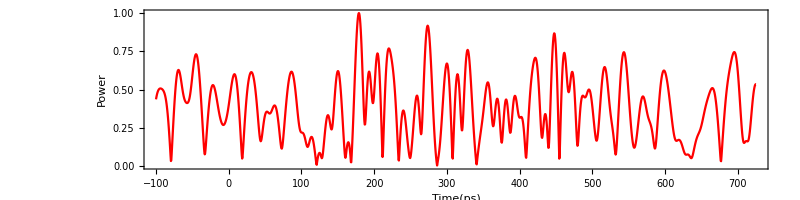

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

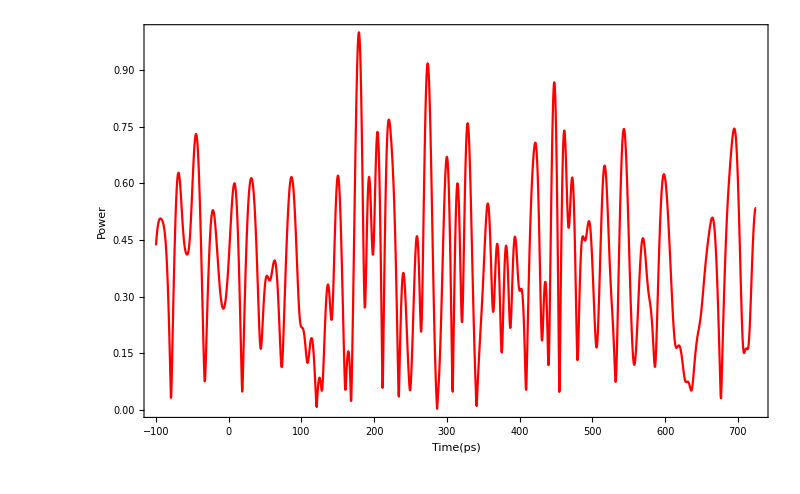

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

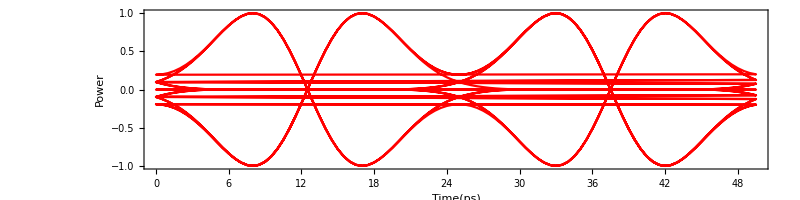

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

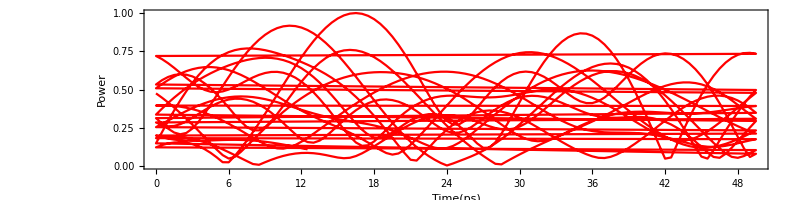

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 20 point

0 is 112 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.583317

Average of 0 is 0.274658

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.0390589

A Standard Deviation of 0 is 0.127209

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-73091.7]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

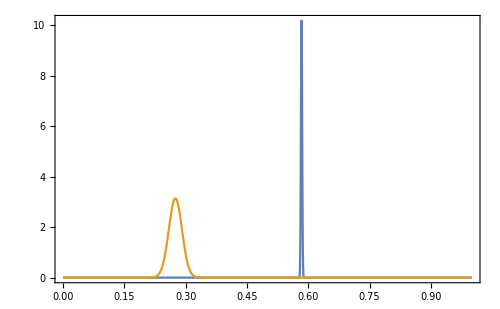

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 1.8564

Q-dB is 5.37344 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.0316982

Eye Opening is 0.461323

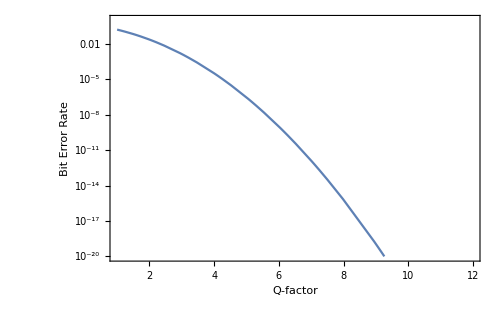

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```